Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Fixed Length Trajectories

```mathematica
currentDir = SetDirectory[NotebookDirectory[]];
$Path=AppendTo[$Path,currentDir];
Needs["packageFixAutocorrelations`"]
?"packageFixAutocorrelations`*"
```

## Interesting Plots

```mathematica
Clear[τ,r,ϕ,θ,ρ, tf, steps, dtau, traj, rate, j , k, μ, ν, pacc, minT, maxT];
tf = 50; (* length to plot along t-axis set as constant for each plot comparison *)
minT = -π/2 (* min angle *);
maxT = 5π/2(* max angle *);
```

## Integrated Autocorrelations

### GHMC vs. θ for fixed τ

The integrated autocorrelation under unit acceptance varying with mixing angle,

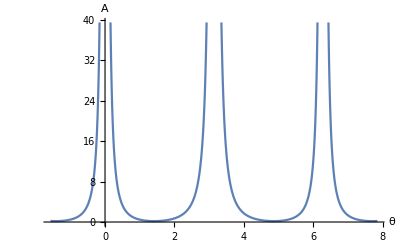

```mathematica
Clear[traj, steps, dtau,θ, phi];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
Plot[ighmc1Acc[phi, θ], {θ, minT, maxT},AxesLabel->{"θ","A"}]
```

### KMC vs. θ and ρ for fixed τ

The integrated autocorrelation varying with mixing angle,

```mathematica
Clear[traj, steps, dtau,θ, phi];
steps = 1;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
Plot3D[ighmc[phi, θ, ρ], {ρ, 0, 1}, {θ, minT, maxT},AxesLabel->{"ρ","θ","A"}]
```

-Graphics3D-

### GHMC vs. ρ for fixed τ

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

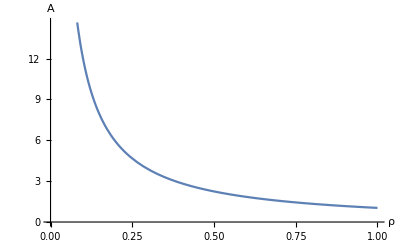

```mathematica
Clear[traj, steps, dtau,θ, phi, theta, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
theta =π/4;
Plot[ighmc[phi, theta,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance vs. Mass

Plotting shows the underdamped form for unit mass and averge trajector length τ,

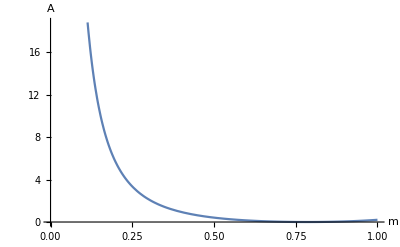

```mathematica
Clear[traj, steps, dtau, t, rate, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;
Plot[ihmc1Acc[traj*m], {m, 0,1},AxesLabel->{"m","A"}]
```

## Autocorrelations (Inverted Laplace Transforms)

These will not return values until a form can be calculated for the acutocorrelation function in Mathmatica.

### GHMC and KHMC both with unit acceptance vs. Ficticious Sample Time, t for fixed ϕ, τ

Comparing HMC and GHMC cases,

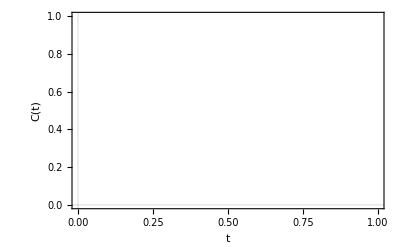

```mathematica
Clear[traj, steps, dtau, t, rate, f1, f2, phi, mass,phiK, trajK, rateK];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
trajK = dtau;
phi = traj*mass;
rate = 1/traj;
rateK = 1/trajK;
phiK = dtau*mass;

f1 = hmc1AccNormalised[t,phi, rate];
f2 =ghmc1AccNormalised[t, phiK, π/6,rateK];

plot1 = Plot[f1,{t,0,tf},
PlotTheme->"Scientific",PlotStyle->Green,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
plot2 =Plot[f2, {t, 0, tf},
PlotTheme->"Scientific",PlotStyle->Dashed,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
Show[plot1,plot2]
```

### HMC vs. ρ and Ficticious Sample Time, t for fixed ϕ, τ

Plotting for varying acceptance rate and smaple time,

```mathematica
Clear[traj, steps, dtau, t, ρ, rate, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;

Plot3D[hmcNormalised[t, phi, ρ,rate], {ρ, 0, 1},{t, 0, tf}, PlotRange->{0,1},AxesLabel->{"ρ","t","C(0)"}]
```

-Graphics3D-

### HMC vs. Ficticious Sample Time, t for fixed ϕ, τ

Plotting for non unit acceptance and a small mass,

```mathematica
Clear[traj, steps, dtau, t, pacc,rate, phi, mass];
steps = 40;
mass = 0.4;
dtau = 1/((3Sqrt[3]-Sqrt[15])*mass/2)/40;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;
pacc = 0.66;

Plot[hmcNormalised[t, phi,pacc, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

-Graphics-